# Variable Moments of Inertia

A numerical implementation of the moments of inertia of a deformed even-even nucleus, which has a near-harmonic shape.
The moments of inertia are considered to change  with respect to a softness parameter C and the ground-state moment of inertia ℐ_0 which is considered as the moment of inertia of an even-even spherically shaped nucleus. Calculations are don based on the work of Mariscotti et. al.

-Graphics-

The cubic equation for ℐ_I:

```mathematica
MOIEQ[x_,I_,i0_,C_]:=x^3-x^2*i0-((I(I+1))/(2C));
moisol[I_,i0_,C_]:=Values@Solve[MOIEQ[x,I,i0,C]==0,x,Reals][[1,1]];
En[I_,i0_,C_]:=N[((I(I+1))/(2*moisol[I,i0,C]))*(1+((I(I+1))/(4*C*moisol[I,i0,C]^3)))];
```

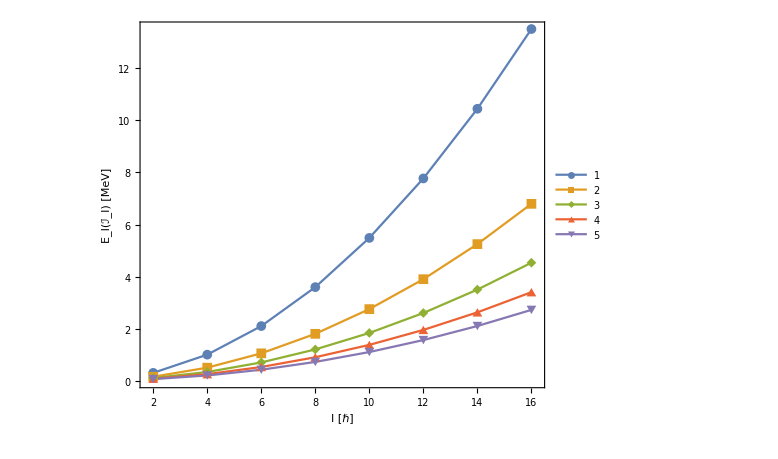

```mathematica
ListPlot[Table[Table[{i,En[i,k,10]},{i,2,16,2}],{k,10,50,10}],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->Large,FrameStyle->Directive[Black,Thick],Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->{{1.8,16.2},Full},PlotLegends->Automatic,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"I [ℏ]","E_I(ℐ_I) [MeV]"}]
```

### Working with the Energy-ratios R_I=E_I/E_2 and MOI’s ratios r_I=ℐ_I/ℐ_0

```mathematica
Rlimits[I_]:={(1/6 I(I+1))^(2/3),1/6 I(I+1)};
```

```mathematica
rRatio[I_,i0_,C_]:=moisol[I,i0,C]/i0;
eqRatio[I_,i0_,C_]:=N[Values@Solve[rRatio[I,i0,C]^3-rRatio[I,i0,C]^2==x*I*(I+1),x,Reals][[1,1]]];
rSols[I_,i0_,C_]:=N[Values@Solve[rRatio[I,i0,C]^3-rRatio[I,i0,C]^2==x*I(I+1),x,Reals][[1,1]]];
Eri[I_,i0_,ri_]:=(I(I+1))/(4i0)*(3ri-1)/ri^2;
RRatio
```

```mathematica
eqRatio[#,1,2]&/@spins
```

{0.25,0.25,0.25,0.25,0.25}

```mathematica
N[Solve[eqRatio[2,i0,c]==ybEnExp[[1]]&&eqRatio[4,i0,c]==ybEnExp[[2]],{i0,c}]]
```

{}

```mathematica
Eri[2,paramsExp[[1]],rSols[2,paramsExp[[1]],paramsExp[[2]]]]
```

0.00629362

### Numerical calculations

Energies of the rotational band in Yb^162

```mathematica
ybEnExp={166.5,486.7,922.9,1444.1,2013.5}/1000;
spins=Table[2*i,{i,1,Length[ybEnExp]}];
dataExp=Table[{spins[[i]],ybEnExp[[i]]},{i,1,Length[spins]}];
paramsExp={0.0164,2.60,0.043};(*The three parameters, namely Subscript[ℐ, 0], C, and σ*)
```

```mathematica
dataExp
```

{{2,0.1665},{4,0.4867},{6,0.9229},{8,1.4441},{10,2.0135}}

```mathematica
FindFit[dataExp,En[x,a,1],a,x]
```

Power::infy: Infinite expression 1/0. encountered.

FindFit::nrlnum: The function value {ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity} is not a list of real numbers with dimensions {5} at {a} = {1.}.

FindFit[{{2,0.1665},{4,0.4867},{6,0.9229},{8,1.4441},{10,2.0135}},ComplexInfinity,a,x]

```mathematica
En[#,1,1]&/@spins[[1]]
```

2

```mathematica
En[spins[[1]],1,1]
```

1.98269